The initial values of v0 that bracket the desired result are {-11,-10}

One Linear Interpolation produces an absolute error for u[L] of 0.00166967

Two Linear Interpolations produce an absolute error for u[L] of 0.0000113615 , where -10.3306  is the estimate for v0.

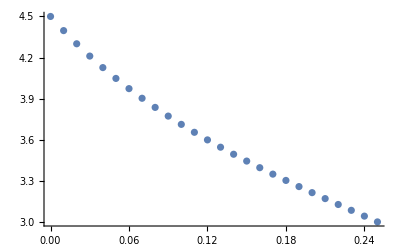

```mathematica
(* Michael Barile 
MATH 68500
11_22_17 *)

(* Section 6.3, Problem #1 *)
(* Shooting Method *)

T=3.0;
k=0.23;
L=0.25;
u0=4.5;
deltax=.01;

(* Iterating through initial values for v0 starting at j=-100 until we find solutions that bracket u[L]=3 *)

For[j=-100,j≤-2,++j;
uvec={u0};uvec1={u0};
vvec={j};
vvec1={j+1};
For[i=1,i≤25,++i,AppendTo[vvec,vvec[[i]]+k*((uvec[[i]]+vvec[[i]]*deltax/2)^4-T^4)*deltax];
AppendTo[uvec,uvec[[i]]+vvec[[i]]*deltax];
AppendTo[vvec1,vvec1[[i]]+k*((uvec1[[i]]+vvec1[[i]]*deltax/2)^4-T^4)*deltax];
AppendTo[uvec1,uvec1[[i]]+vvec1[[i]]*deltax];
];
If[(3-uvec[[Length[uvec]]])*(3-uvec1[[Length[uvec1]]])<0,
Print["The initial values of v0 that bracket the desired result are ",{j, j+1}];
Break[]
];
];

(* First Linear Interpolation *)

v0=j+(3-uvec[[Length[uvec]]])*((j+1)-j)/(uvec1[[Length[uvec1]]]-uvec[[Length[uvec]]]);
uvec2={u0};
vvec2={v0};
For[i=1,i≤25,++i,AppendTo[vvec2,vvec2[[i]]+k*((uvec2[[i]]+vvec2[[i]]*deltax/2)^4-T^4)*deltax];
AppendTo[uvec2,uvec2[[i]]+vvec2[[i]]*deltax];
];
Print["One Linear Interpolation produces an absolute error for u[L] of ",Abs[3-uvec2[[Length[uvec2]]]]];

(* Second Linear Interpolation *)

v0=v0+(3-uvec2[[Length[uvec2]]])*((j+1)-v0)/(uvec1[[Length[uvec1]]]-uvec2[[Length[uvec2]]]);
uvec2={u0};
vvec2={v0};
For[i=1,i≤25,++i,AppendTo[vvec2,vvec2[[i]]+k*((uvec2[[i]]+vvec2[[i]]*deltax/2)^4-T^4)*deltax];
AppendTo[uvec2,uvec2[[i]]+vvec2[[i]]*deltax];
];
Print["Two Linear Interpolations produce an absolute error for u[L] of ",Abs[3-uvec2[[Length[uvec2]]]]", where ", v0" is the estimate for v0."];

listuvec2={};
For[i=1,i≤Length[uvec],++i,
AppendTo[listuvec2,{deltax*(i-1),uvec2[[i]]}]
];
ListPlot[listuvec2]
```

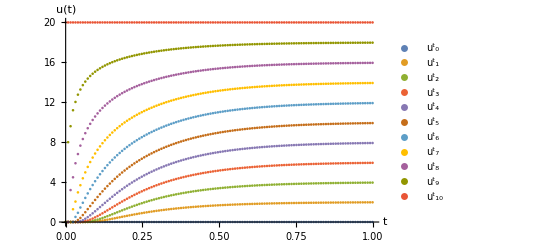

```mathematica
(* Section 6.4, Problem #1 *)
(* method of lines, forward Euler *)

(* rod of length 1, deltax = 0.1, time interval of length 1, time steps of .008 *)
alpha=1/2;
deltax=.1;
deltat=.008;
lambda=alpha*deltat/deltax^2;
T=1;

For[i=1,i≤11,++i,
If[i==11,
Subscript[(u^0), i-1]=20,
Subscript[(u^0), i-1]=0
];
];

(* j time steps, i through positions *)

For[j=1,j≤T/deltat,++j,
For[i=0,i≤10,++i,
If[i==10,
Subscript[(u^j), i]=20,
If[i==0,
Subscript[(u^j), i]=0,
Subscript[(u^j), i]=Subscript[(u^(j-1)), i]+lambda*(Subscript[(u^(j-1)), i+1]-2*Subscript[(u^(j-1)), i]+Subscript[(u^(j-1)), i-1])
];
];
];
];

(* storing vectors with heat values at fixed position j along rod, where time ranges from 0 to 1 in steps of .008 *)
uvec={};
For[j=0,j≤10,++j,
Subscript[uvec, j]={};
For[i=0,i≤T/deltat,++i,
AppendTo[Subscript[uvec, j],Subscript[(u^i), j]]
];
AppendTo[uvec,Subscript[uvec, j]]
];

tvec={};
For[i=1,i≤T/deltat+1,++i,
AppendTo[tvec,deltat*(i-1)]
];

listplots={};
For[j=1,j≤11,++j,
list={};
For[i=1,i≤T/deltat+1,++i,
AppendTo[list,{tvec[[i]],uvec[[j]][[i]]}]
];
AppendTo[listplots,list]
];

ListPlot[listplots,AxesLabel->{t,u[t]},PlotLegends->{Subscript[(u^t), 0],Subscript[(u^t), 1],Subscript[(u^t), 2],Subscript[(u^t), 3],Subscript[(u^t), 4],Subscript[(u^t), 5],Subscript[(u^t), 6],Subscript[(u^t), 7],Subscript[(u^t), 8],Subscript[(u^t), 9],Subscript[(u^t), 10]}]
```

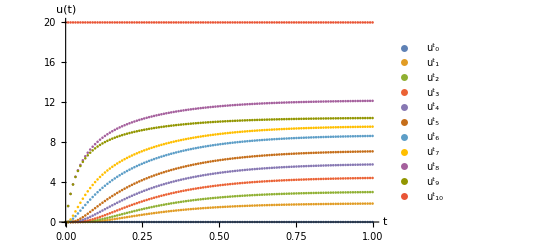

```mathematica
(* Section 6.4, Problem #3 *)

alpha=1/2;
deltax=.1;
deltat=.008;
lambda=alpha*deltat/deltax^2;
T=1;
tvec={};

xvec={};
For[i=1,i≤11,++i,
AppendTo[xvec,(i-1)*deltax]
];

For[i=1,i≤T/deltat+1,++i,
AppendTo[tvec,deltat*(i-1)]
];

(* initializing Subscript[(u^0), i], including Subscript[(u^0), -1]_ and Subscript[(u^0), 11] value, set to 0 for all times n, for ease of coding  *)

For[i=0,i≤12,++i,
If[i==11,
Subscript[(u^0), i-1]=20,
Subscript[(u^0), i-1]=0
];
];

For[j=1,j≤T/deltat,++j,
For[i=-1,i≤11,++i,
If[i==10,
Subscript[(u^j), i]=20,
If[i==0||i==-1||i==11,
Subscript[(u^j), i]=0,
Subscript[(u^(j-1/2)), i-1]=Subscript[(u^(j-1)), i-1]+alpha/deltax^2*(Subscript[(u^(j-1)), i]-2*Subscript[(u^(j-1)), i-1]+Subscript[(u^(j-1)), i-2])*deltat/2;
Subscript[(u^(j-1/2)), i]=Subscript[(u^(j-1)), i]+alpha/deltax^2*(Subscript[(u^(j-1)), i+1]-2*Subscript[(u^(j-1)), i]+Subscript[(u^(j-1)), i-1])*deltat/2;
Subscript[(u^(j-1/2)), i+1]=Subscript[(u^(j-1)), i+1]+alpha/deltax^2*(Subscript[(u^(j-1)), i+2]-2*Subscript[(u^(j-1)), i+1]+Subscript[(u^(j-1)), i])*deltat/2;
Subscript[(u^j), i]=Subscript[(u^(j-1)), i]+alpha/deltax^2*(Subscript[(u^(j-1/2)), i+1]-2*Subscript[(u^(j-1/2)), i]+Subscript[(u^(j-1/2)), i-1])*deltat
];
];
];
];

(* storing vectors with heat values at fixed position j along rod, where time ranges from 0 to 1 in steps of .008 *)
uvec={};
For[j=0,j≤10,++j,
Subscript[uvec, j]={};
For[i=0,i≤T/deltat,++i,
AppendTo[Subscript[uvec, j],Subscript[(u^i), j]]
];
AppendTo[uvec,Subscript[uvec, j]]
];

tvec={};
For[i=1,i≤T/deltat+1,++i,
AppendTo[tvec,deltat*(i-1)]
];

listplots={};
For[j=1,j≤11,++j,
list={};
For[i=1,i≤T/deltat+1,++i,
AppendTo[list,{tvec[[i]],uvec[[j]][[i]]}]
];
AppendTo[listplots,list]
];

ListPlot[listplots,AxesLabel->{t,u[t]},PlotLegends->{Subscript[(u^t), 0],Subscript[(u^t), 1],Subscript[(u^t), 2],Subscript[(u^t), 3],Subscript[(u^t), 4],Subscript[(u^t), 5],Subscript[(u^t), 6],Subscript[(u^t), 7],Subscript[(u^t), 8],Subscript[(u^t), 9],Subscript[(u^t), 10]}]
```

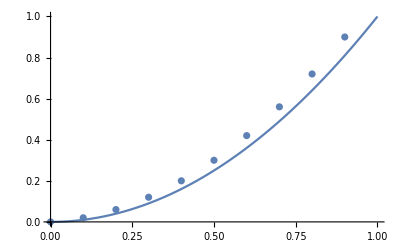

```mathematica
(* Some extra simpler things to get used to forward euler and midpoint method *)

(* Forward Euler applied to dy/dx=2x, y(0)=0 (so y=x^2)*)
deltax=.1;
x[t_]=deltax*t;
xmid[t_]=deltax*t+deltax/2;
dy[x_]=2*x;
xvec={};
For[i=0,i≤10,++i,
AppendTo[xvec,x[i]]
];
Subscript[y, 0]=0;
yvec={Subscript[y, 0]};
For[i=1,i≤10,++i,
Subscript[y, i]=Subscript[y, i-1]+dy[xvec[[i+1]]]*deltax;
AppendTo[yvec,Subscript[y, i]]
];
list={};
For[i=1,i≤Length[yvec],++i,
AppendTo[list,{xvec[[i]],yvec[[i]]}]
];
Show[{Plot[x^2,{x,0,1}],ListPlot[list]}]
```

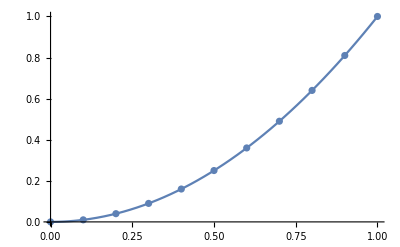

```mathematica
(* midpoint method applied to same as above, results clearly better *)
Subscript[y, 0]=0;
Subscript[y, 1]=Subscript[y, 0]+2*(0+deltax/2)*deltax;
Subscript[x, 0]=0;
xvec={Subscript[x, 0]};
For[i=1,i≤10,++i,
Subscript[x, i]=deltax*i;
AppendTo[xvec,Subscript[x, i]]
];
yvec={Subscript[y, 0]};
For[i=1,i≤10,++i,
Subscript[y, i]=Subscript[y, i-1]+dy[xvec[[i]]+deltax/2]*deltax;
AppendTo[yvec,Subscript[y, i]]
];
list={};
For[i=1,i≤Length[yvec],++i,
AppendTo[list,{xvec[[i]],yvec[[i]]}]
];
Show[{Plot[x^2,{x,0,1}],ListPlot[list]}]
```

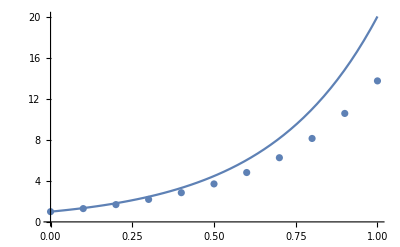

```mathematica
(* exponent function, forward euler *)
y[x_]:=Exp[3x];
dy[x_]=3*y[x];
Subscript[y, 0]=1;
Subscript[y, 1]=Subscript[y, 0]+3*Subscript[y, 0]*deltax;
Subscript[y, 2]=Subscript[y, 1]+3*Subscript[y, 1]*deltax;
yvec={Subscript[y, 0]};
For[i=1,i≤10,++i,
Subscript[y, i]=Subscript[y, i-1]+3*Subscript[y, i-1]*deltax;
AppendTo[yvec,Subscript[y, i]]
];
list={};
For[i=1,i≤Length[yvec],++i,
AppendTo[list,{xvec[[i]],yvec[[i]]}]
];
Show[{Plot[Exp[3*x],{x,0,1}],ListPlot[list]}]
```

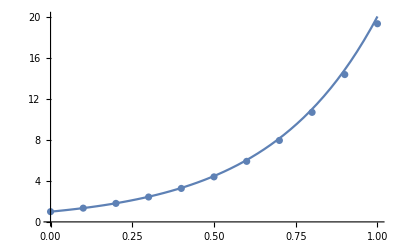

```mathematica
(* exponent function, midpoint method *)

Subscript[y, 0]=1;
yvec={Subscript[y, 0]};
For[i=1,i≤10,++i,
Subscript[y, i]=Subscript[y, i-1]+3*(Subscript[y, i-1]+3*Subscript[y, i-1]*deltax/2)*deltax;
AppendTo[yvec,Subscript[y, i]]
];
yvec;
list={};
For[i=1,i≤Length[yvec],++i,
AppendTo[list,{xvec[[i]],yvec[[i]]}]
];
Show[{Plot[Exp[3*x],{x,0,1}],ListPlot[list]}]
```

```mathematica
(* I am leaving this section here, commented out.  This is the calculation for Subscript[(u^1), j] for each position j=1,2,...9 along the rod using the midpoint method, written out explicitly.  It's coded as a nested loop above, going through all time steps n.  Note the use of Subscript[(u^0), -1]=0 and Subscript[(u^0), 11]=0 to simplify the coding.  Subscript[(u^n), -1]and Subscript[(u^n), 11] are set to 0 for all time steps n. *)  

(*
Subscript[(u^(1/2)), 0]=Subscript[(u^0), 0]+alpha/deltax^2*(Subscript[(u^0), 1]-2*Subscript[(u^0), 0]+Subscript[(u^0), -1])*deltat/2;
Subscript[(u^(1/2)), 1]=Subscript[(u^0), 1]+alpha/deltax^2*(Subscript[(u^0), 2]-2*Subscript[(u^0), 1]+Subscript[(u^0), 0])*deltat/2;
Subscript[(u^(1/2)), 2]=Subscript[(u^0), 2]+alpha/deltax^2*(Subscript[(u^0), 3]-2*Subscript[(u^0), 2]+Subscript[(u^0), 1])*deltat/2;
Subscript[(u^1), 1]=Subscript[(u^0), 1]+alpha/deltax^2*(Subscript[(u^(1/2)), 2]-2*Subscript[(u^(1/2)), 1]+Subscript[(u^(1/2)), 0])*deltat

Subscript[(u^(1/2)), 1]=Subscript[(u^0), 1]+alpha/deltax^2*(Subscript[(u^0), 2]-2*Subscript[(u^0), 1]+Subscript[(u^0), 0])*deltat/2;
Subscript[(u^(1/2)), 2]=Subscript[(u^0), 2]+alpha/deltax^2*(Subscript[(u^0), 3]-2*Subscript[(u^0), 2]+Subscript[(u^0), 1])*deltat/2;
Subscript[(u^(1/2)), 3]=Subscript[(u^0), 3]+alpha/deltax^2*(Subscript[(u^0), 4]-2*Subscript[(u^0), 3]+Subscript[(u^0), 2])*deltat/2;
Subscript[(u^1), 2]=Subscript[(u^0), 2]+alpha/deltax^2*(Subscript[(u^(1/2)), 3]-2*Subscript[(u^(1/2)), 2]+Subscript[(u^(1/2)), 1])*deltat

Subscript[(u^(1/2)), 2]=Subscript[(u^0), 2]+alpha/deltax^2*(Subscript[(u^0), 3]-2*Subscript[(u^0), 2]+Subscript[(u^0), 1])*deltat/2;
Subscript[(u^(1/2)), 3]=Subscript[(u^0), 3]+alpha/deltax^2*(Subscript[(u^0), 4]-2*Subscript[(u^0), 3]+Subscript[(u^0), 2])*deltat/2;
Subscript[(u^(1/2)), 4]=Subscript[(u^0), 4]+alpha/deltax^2*(Subscript[(u^0), 5]-2*Subscript[(u^0), 4]+Subscript[(u^0), 3])*deltat/2;
Subscript[(u^1), 3]=Subscript[(u^0), 3]+alpha/deltax^2*(Subscript[(u^(1/2)), 4]-2*Subscript[(u^(1/2)), 3]+Subscript[(u^(1/2)), 2])*deltat

Subscript[(u^(1/2)), 3]=Subscript[(u^0), 3]+alpha/deltax^2*(Subscript[(u^0), 4]-2*Subscript[(u^0), 3]+Subscript[(u^0), 2])*deltat/2;
Subscript[(u^(1/2)), 4]=Subscript[(u^0), 4]+alpha/deltax^2*(Subscript[(u^0), 5]-2*Subscript[(u^0), 4]+Subscript[(u^0), 3])*deltat/2;
Subscript[(u^(1/2)), 5]=Subscript[(u^0), 5]+alpha/deltax^2*(Subscript[(u^0), 6]-2*Subscript[(u^0), 5]+Subscript[(u^0), 4])*deltat/2;
Subscript[(u^1), 4]=Subscript[(u^0), 4]+alpha/deltax^2*(Subscript[(u^(1/2)), 5]-2*Subscript[(u^(1/2)), 4]+Subscript[(u^(1/2)), 3])*deltat

Subscript[(u^(1/2)), 4]=Subscript[(u^0), 4]+alpha/deltax^2*(Subscript[(u^0), 5]-2*Subscript[(u^0), 4]+Subscript[(u^0), 3])*deltat/2;
Subscript[(u^(1/2)), 5]=Subscript[(u^0), 5]+alpha/deltax^2*(Subscript[(u^0), 6]-2*Subscript[(u^0), 5]+Subscript[(u^0), 4])*deltat/2;
Subscript[(u^(1/2)), 6]=Subscript[(u^0), 6]+alpha/deltax^2*(Subscript[(u^0), 7]-2*Subscript[(u^0), 6]+Subscript[(u^0), 5])*deltat/2;
Subscript[(u^1), 5]=Subscript[(u^0), 5]+alpha/deltax^2*(Subscript[(u^(1/2)), 6]-2*Subscript[(u^(1/2)), 5]+Subscript[(u^(1/2)), 4])*deltat

Subscript[(u^(1/2)), 5]=Subscript[(u^0), 5]+alpha/deltax^2*(Subscript[(u^0), 6]-2*Subscript[(u^0), 5]+Subscript[(u^0), 4])*deltat/2;
Subscript[(u^(1/2)), 6]=Subscript[(u^0), 6]+alpha/deltax^2*(Subscript[(u^0), 7]-2*Subscript[(u^0), 6]+Subscript[(u^0), 5])*deltat/2;
Subscript[(u^(1/2)), 7]=Subscript[(u^0), 7]+alpha/deltax^2*(Subscript[(u^0), 8]-2*Subscript[(u^0), 7]+Subscript[(u^0), 6])*deltat/2;
Subscript[(u^1), 6]=Subscript[(u^0), 6]+alpha/deltax^2*(Subscript[(u^(1/2)), 7]-2*Subscript[(u^(1/2)), 6]+Subscript[(u^(1/2)), 5])*deltat

Subscript[(u^(1/2)), 6]=Subscript[(u^0), 6]+alpha/deltax^2*(Subscript[(u^0), 7]-2*Subscript[(u^0), 6]+Subscript[(u^0), 5])*deltat/2;
Subscript[(u^(1/2)), 7]=Subscript[(u^0), 7]+alpha/deltax^2*(Subscript[(u^0), 8]-2*Subscript[(u^0), 7]+Subscript[(u^0), 6])*deltat/2;
Subscript[(u^(1/2)), 8]=Subscript[(u^0), 8]+alpha/deltax^2*(Subscript[(u^0), 9]-2*Subscript[(u^0), 8]+Subscript[(u^0), 7])*deltat/2;
Subscript[(u^1), 7]=Subscript[(u^0), 7]+alpha/deltax^2*(Subscript[(u^(1/2)), 8]-2*Subscript[(u^(1/2)), 7]+Subscript[(u^(1/2)), 6])*deltat

Subscript[(u^(1/2)), 7]=Subscript[(u^0), 7]+alpha/deltax^2*(Subscript[(u^0), 8]-2*Subscript[(u^0), 7]+Subscript[(u^0), 6])*deltat/2;
Subscript[(u^(1/2)), 8]=Subscript[(u^0), 8]+alpha/deltax^2*(Subscript[(u^0), 9]-2*Subscript[(u^0), 8]+Subscript[(u^0), 7])*deltat/2;
Subscript[(u^(1/2)), 9]=Subscript[(u^0), 9]+alpha/deltax^2*(Subscript[(u^0), 10]-2*Subscript[(u^0), 9]+Subscript[(u^0), 8])*deltat/2;
Subscript[(u^1), 8]=Subscript[(u^0), 8]+alpha/deltax^2*(Subscript[(u^(1/2)), 9]-2*Subscript[(u^(1/2)), 8]+Subscript[(u^(1/2)), 7])*deltat

Subscript[(u^(1/2)), 8]=Subscript[(u^0), 8]+alpha/deltax^2*(Subscript[(u^0), 9]-2*Subscript[(u^0), 8]+Subscript[(u^0), 7])*deltat/2;
Subscript[(u^(1/2)), 9]=Subscript[(u^0), 9]+alpha/deltax^2*(Subscript[(u^0), 10]-2*Subscript[(u^0), 9]+Subscript[(u^0), 8])*deltat/2;
Subscript[(u^(1/2)), 10]=Subscript[(u^0), 10]+alpha/deltax^2*(Subscript[(u^0), 11]-2*Subscript[(u^0), 10]+Subscript[(u^0), 9])*deltat/2;
Subscript[(u^1), 9]=Subscript[(u^0), 9]+alpha/deltax^2*(Subscript[(u^(1/2)), 10]-2*Subscript[(u^(1/2)), 9]+Subscript[(u^(1/2)), 8])*deltat  *)
```